# Cost of Dai Collateral Attack

```mathematica
LiquidationThreshold = 1.5;
DaiCirculation =77000000;
EthCollateral = 355000000;
KeeperDiscount = 0.03;
AvgTxPrice = 0.20;
CDPClosingNumTx = 6;
PETHEx = 1.04;
```

## Required collateral to decrease system collateral ratio

```mathematica
collateral[target_, CDPratio_] = (EthCollateral - target * DaiCirculation) / (target - CDPratio);
```

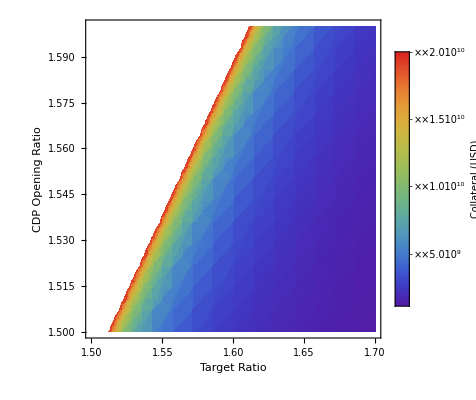

```mathematica
min = 0;
max = 2*10^10;
DensityPlot[collateral[t,r],{t,1.5,1.7}, {r,1.5,1.6},FrameLabel->{"Target Ratio", "CDP Opening Ratio"}, PlotLegends-> BarLegend[Automatic, LegendLabel->"Collateral (USD)"], PlotRange->{min,max}, PlotTheme->"Monochrome",ColorFunctionScaling->False, ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&),MeshFunctions->{#3 &}, Mesh->9]
```

## Cost for decreasing collateral ratio

```mathematica
cost[maxCDP_,target_] = collateral[target,1.5] / maxCDP * AvgTxPrice;
```

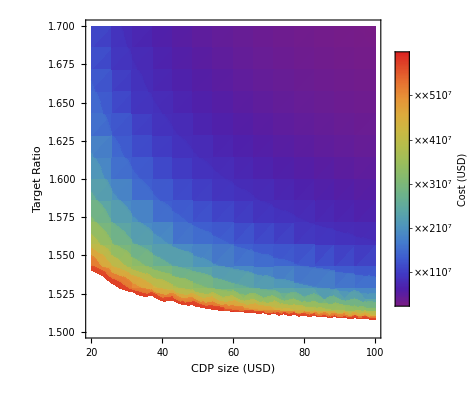

```mathematica
DensityPlot[cost[c,t],{c, 20, 100},{t, 1.5, 1.7}, FrameLabel->{"CDP size (USD)", "Target Ratio"}, PlotLegends-> BarLegend[Automatic, LegendLabel->"Cost (USD)"], PlotTheme->"Monochrome", ColorFunction->"Rainbow", MeshFunctions->{#3 &}, Mesh->9]
```